```mathematica
Amat[β_,κ_]:=Table[KroneckerDelta[i,j]+β[[i]]/(κ[[i]]+κ[[j]])Exp[8 κ[[i]]^3 t-(κ[[i]]+κ[[j]])x],{i,1,Length[κ]},{j,1,Length[κ]}]
```

```mathematica
solitary[β_,κ_]:=-2 D[Log[Det[Amat[β,κ]]],{x,2}]
```

```mathematica
β1={1,2};
```

```mathematica
κ1={1/10,5/10};
```

```mathematica
s1=solitary[β1,κ1]
```

-2 (-((-16/3 ⅇ^((126 t)/125-(6 x)/5)-2 ⅇ^(t-x)-ⅇ^(t/125-x/5))^2)/((1+40/9 ⅇ^((126 t)/125-(6 x)/5)+2 ⅇ^(t-x)+5 ⅇ^(t/125-x/5))^2)+(32/5 ⅇ^((126 t)/125-(6 x)/5)+2 ⅇ^(t-x)+1/5 ⅇ^(t/125-x/5))/(1+40/9 ⅇ^((126 t)/125-(6 x)/5)+2 ⅇ^(t-x)+5 ⅇ^(t/125-x/5)))

```mathematica
s1//FullSimplify
```

-(18 ⅇ^(1/125 (t+25 x)) (16 ⅇ^(2 t)+1000 ⅇ^((126 t)/125+(4 x)/5)+9 ⅇ^(2 x)+576 ⅇ^(t+x)+90 ⅇ^((124 t)/125+(6 x)/5)))/(5 (40 ⅇ^(126 t/125)+18 ⅇ^(t+x/5)+9 ⅇ^(6 x/5)+45 ⅇ^(t/125+x))^2)

```mathematica
Plot3D[s1,{x,-10,10},{t,0,1},PlotRange->All,PlotPoints->100]
```

-Graphics3D-

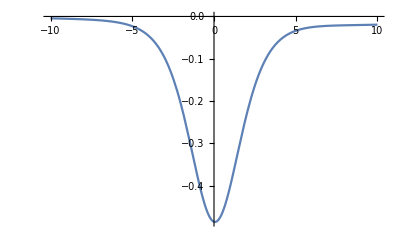

```mathematica
Plot[s1/.t->0,{x,-10,10}]
```

```mathematica
s1/.t->0//FullSimplify
```

-(18 ⅇ^(x/5) (16+1000 ⅇ^(4 x/5)+576 ⅇ^x+90 ⅇ^(6 x/5)+9 ⅇ^(2 x)))/(5 (40+9 ⅇ^(x/5) (2+5 ⅇ^(4 x/5)+ⅇ^x))^2)

```mathematica
s1/.x->-10//FullSimplify
```

-(18 ⅇ^(2+t/125) (9+90 ⅇ^(8+(124 t)/125)+576 ⅇ^(10+t)+1000 ⅇ^(12+(126 t)/125)+16 ⅇ^(20+2 t)))/(5 (9+45 ⅇ^(2+t/125)+18 ⅇ^(10+t)+40 ⅇ^(12+(126 t)/125))^2)

```mathematica
s1/.x->10//FullSimplify
```

-(18 ⅇ^(2+t/125) (9 ⅇ^20+90 ⅇ^(12+(124 t)/125)+16 ⅇ^(2 t)+576 ⅇ^(10+t)+1000 ⅇ^(8+(126 t)/125)))/(5 (9 ⅇ^12+45 ⅇ^(10+t/125)+40 ⅇ^(126 t/125)+18 ⅇ^(2+t))^2)

```mathematica
s1//FullSimplify//InputForm
```

-((18*E^((1/125)*(t + 25*x))*(16*E^(2*t) + 1000*E^((126*t)/125 + (4*x)/5) + 9*E^(2*x) + 576*E^(t + x) + 90*E^((124*t)/125 + (6*x)/5)))/(5*(40*E^((126*t)/125) + 18*E^(t + x/5) + 9*E^((6*x)/5) + 45*E^(t/125 + x))^2))

```mathematica
D[s1,x]//FullSimplify//InputForm
```

(18 ⅇ^(1/125 (t+25 x)) (-640 ⅇ^(376 t/125)+288 ⅇ^(3 t+x/5)-200000 ⅇ^((252 t)/125+(4 x)/5)+81 ⅇ^(16 x/5)-185760 ⅇ^((251 t)/125+x)-65088 ⅇ^(2 t+(6 x)/5)-8100 ⅇ^((249 t)/125+(7 x)/5)+225000 ⅇ^((127 t)/125+(9 x)/5)+162720 ⅇ^((126 t)/125+2 x)+41796 ⅇ^(t+(11 x)/5)-405 ⅇ^(t/125+3 x)+4050 ⅇ^(4/125 (31 t+75 x))))/(25 (40 ⅇ^(126 t/125)+18 ⅇ^(t+x/5)+9 ⅇ^(6 x/5)+45 ⅇ^(t/125+x))^3)

```mathematica
(18*E^((1/125)*(t + 25*x))*(-640*E^((376*t)/125) + 288*E^(3*t + x/5) - 200000*E^((252*t)/125 + (4*x)/5) + 81*E^((16*x)/5) - 185760*E^((251*t)/125 + x) - 65088*E^(2*t + (6*x)/5) - 8100*E^((249*t)/125 + (7*x)/5) + 225000*E^((127*t)/125 + (9*x)/5) + 
    162720*E^((126*t)/125 + 2*x) + 41796*E^(t + (11*x)/5) - 405*E^(t/125 + 3*x) + 4050*E^((4/125)*(31*t + 75*x))))/(25*(40*E^((126*t)/125) + 18*E^(t + x/5) + 9*E^((6*x)/5) + 45*E^(t/125 + x))^3)
```